```mathematica
oeisPage[n_]:=URLFetch["http://oeis.org/search?q=seq:"<>ToString[n]<>"&fmt=data"]
oeis[n_]:=Block[{p,m1,m2},
p=oeisPage[n];m1=StringCases[p,"Found "~~m:NumberString~~" results, too many to show":>m];m2=StringCases[p,"Displaying 1-"~~NumberString~~" of "~~m:NumberString~~" result":>m];
If[Length[m2]==0,If[Length[m1]==0,
0,
FromDigits[m1[[1]]]],
FromDigits[m2[[1]]]]]
oeisFound[n_]:=Length[StringCases[oeisPage[n],"Sorry, but the terms do not match anything in the table"]]!=0
score[n_]:=n*oeis[n]
```

```mathematica
AbsoluteTiming[hund={oeis[#],Pause[1]}[[1]]&/@Range[100];]
```

{371.75069,Null}

```mathematica
StringCases[oeisPage[790],"Displaying 1-"~~NumberString~~" of "~~m:NumberString~~" result":>m]
```

{393}

```mathematica
AbsoluteTiming[(thou[#]=oeis[#];Pause[5];)&/@Range[1000];]
```

{6196.73077,Null}

```mathematica
Save["oeis1000.m",oeis1000]
```

```mathematica
oeis1000=Prepend[thou/@Range[1000],oeis[0]];
```

```mathematica
hundscore=N[hund*Range[100]];
Position[hundscore,Max[hundscore]]
Position[hundscore,#]&/@Sort[hundscore]//Flatten
```

{{64}}

{1,2,3,4,5,6,10,7,14,11,8,12,9,13,15,18,17,22,16,19,26,20,21,27,23,25,38,34,33,39,28,24,29,46,35,86,94,30,74,87,92,32,82,44,95,93,98,51,31,58,52,69,68,76,62,50,75,40,37,45,77,42,78,49,57,88,54,85,43,47,41,99,65,36,48,66,53,91,55,59,70,63,83,80,67,79,56,84,90,96,81,61,71,73,72,60,100,97,89,64}

```mathematica
score/@Range[1725,1730]
```

{255300,214024,303952,1505088,871416,294100}

```mathematica
score[2^32+#]&/@Range[0,9]
```

{932007903232,214748364850,12884901894,17179869196,8589934600,4294967301,0,12884901909,4294967304,8589934610}

```mathematica
623094791644755
```

```mathematica
64*oeis[64]
```

1150272

```mathematica
Range[0,10]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Sort[oeis1000][[1;;10]]
```

{260,282,290,292,293,295,296,300,304,307}

```mathematica
Flatten[Position[oeis1000,#]&/@%69]-1
```

{934,958,955,974,994,998,956,933,982,921}

```mathematica
Flatten[Position[oeis1000*Range[0,1000],#]&/@%64]-1
```

{0,1,2,934,3,958,796,830,695,802}

```mathematica
oeis1000[[935]]
```

260

```mathematica
oeis1000[[721]]*720
```

1913760

```mathematica
6!
```

720

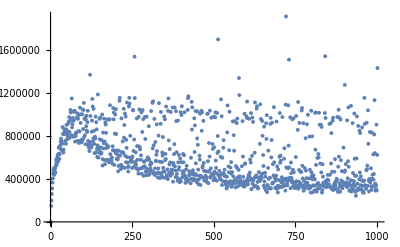

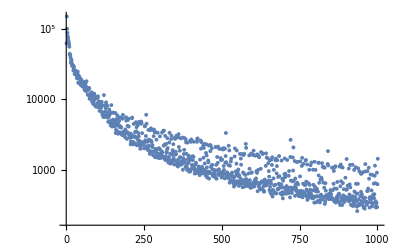

```mathematica
ListPlot[oeis1000*Range[0,1000]]
ListLogPlot[oeis1000]
```

```mathematica
{#+1,Pause[2]}[[1]]&/@Range[3]
```

{2,3,4}

```mathematica
Position[hund,Min[hund]]
```

{{98}}

```mathematica
hund[[98]]
```

7812

```mathematica
oeis[1]
```

148554

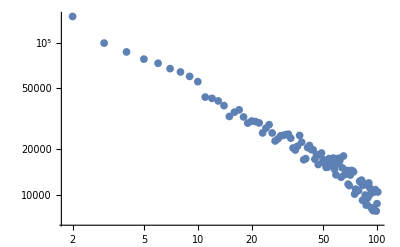

```mathematica
ListLogLogPlot[Prepend[hund,0],PlotRange->All]
```